```mathematica
repcount[list_]:=Length[list]-Length[DeleteDuplicates[list]]
```

```mathematica
Reduce[(k(k+1)(k+2))/3==l&&k>0,Integers]
```

((C[1]∈Integers&&C[1]≥1&&k==3 C[1])||(C[1]∈Integers&&C[1]≥0&&k==1+3 C[1])||(C[1]∈Integers&&C[1]≥0&&k==2+3 C[1]))&&l==1/3 (2 k+3 k^2+k^3)

```mathematica
Monitor[Table[n-1-Max[Table[Mod[2k+1,n],{k,1,n}]],{n,2,20}],n]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Flatten[Position[%,1]]+1
```

{3,6,9,12,15,18}

```mathematica
"(k (k + 3))/2 fails if mod {4,8,16,32,64,128,256,512,1024,2048,4096,8192}"
```

```mathematica
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99}
```

```mathematica
Table[Mod[(k(k+3))/2,5],{k,1,20}]
```

{1,3,1,0,0,1,3,1,0,0,1,3,1,0,0,1,3,1,0,0}

```mathematica
3k +2 k^2
```

```mathematica
2+2 k
```

```mathematica
a[n]==a[n-1]+Mod[a[n-1],q]
```

```mathematica
Table[q-Length[DeleteDuplicates[Map[Mod[#,q]&,RecurrenceTable[{a[n+1]==(a[n]+1)a[n]/2,a[1]==1},a,{n,1,2q}]]]],{q,1,20}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
nester[{s_,ca_,co_,maxd_}]:=Block[{tab=Table[{s[[i]]*ca[[i]],Mod[s[[i]]+ca[[i]],2]},{i,1,maxd}]},{Map[Last,tab],PadRight[Delete[Map[First,tab],1],maxd],co+1,maxd}];
```

```mathematica
Clear[a,b,a0,b0,a1,b1,a2,b2,maxdigits,table,sum,carry]
```

```mathematica
carrylen[a0_,b0_]:=Block[{a1=IntegerDigits[a0,2],b1=IntegerDigits[b0,2],maxdigits=1+Length[IntegerDigits[a0+b0,2]]},
Block[{a2=PadLeft[a1,maxdigits],b2=PadLeft[b1,maxdigits]},
Block[{table=Table[{a2[[i]]*b2[[i]],Mod[a2[[i]]+b2[[i]],2]},{i,1,maxdigits}]},
Block[{sum=Map[Last,table],carry=PadRight[Delete[Map[First,table],1],maxdigits]},NestWhile[nester,{sum,carry,0,maxdigits},(Total[#[[2]]]>0&&#[[3]]<1000)&][[3]]]]]]
```

```mathematica
50*50+100
```

2600

```mathematica
Clear[htable]
```

```mathematica
dtable=Map[PadRight[#,2000]&,table]
```

{1}
 |  |  |  |

```mathematica
Timing[table=Monitor[Table[Table[carrylen[g,h],{g,1,h}],{h,1,2000}],{h}];]
```

{534.7306,Null}

```mathematica
Position[table,Max[Map[Max,table]]]
```

{{1025,1023},{1027,1021},{1029,1019},{1031,1017},{1033,1015},{1035,1013},{1037,1011},{1039,1009},{1041,1007},{1043,1005},{1045,1003},{1047,1001},{1049,999},{1051,997},{1053,995},{1055,993},{1057,991},{1059,989},{1061,987},{1063,985},{1065,983},{1067,981},{1069,979},{1071,977},{1073,975},{1075,973},{1077,971},{1079,969},{1081,967},{1083,965},{1085,963},{1087,961},{1089,959},{1091,957},{1093,955},{1095,953},{1097,951},{1099,949},{1101,947},{1103,945},{1105,943},{1107,941},{1109,939},{1111,937},{1113,935},{1115,933},{1117,931},{1119,929},{1121,927},{1123,925},{1125,923},{1127,921},{1129,919},{1131,917},{1133,915},{1135,913},{1137,911},{1139,909},{1141,907},{1143,905},{1145,903},{1147,901},{1149,899},{1151,897},{1153,895},{1155,893},{1157,891},{1159,889},{1161,887},{1163,885},{1165,883},{1167,881},{1169,879},{1171,877},{1173,875},{1175,873},{1177,871},{1179,869},{1181,867},{1183,865},{1185,863},{1187,861},{1189,859},{1191,857},{1193,855},{1195,853},{1197,851},{1199,849},{1201,847},{1203,845},{1205,843},{1207,841},{1209,839},{1211,837},{1213,835},{1215,833},{1217,831},{1219,829},{1221,827},{1223,825},{1225,823},{1227,821},{1229,819},{1231,817},{1233,815},{1235,813},{1237,811},{1239,809},{1241,807},{1243,805},{1245,803},{1247,801},{1249,799},{1251,797},{1253,795},{1255,793},{1257,791},{1259,789},{1261,787},{1263,785},{1265,783},{1267,781},{1269,779},{1271,777},{1273,775},{1275,773},{1277,771},{1279,769},{1281,767},{1283,765},{1285,763},{1287,761},{1289,759},{1291,757},{1293,755},{1295,753},{1297,751},{1299,749},{1301,747},{1303,745},{1305,743},{1307,741},{1309,739},{1311,737},{1313,735},{1315,733},{1317,731},{1319,729},{1321,727},{1323,725},{1325,723},{1327,721},{1329,719},{1331,717},{1333,715},{1335,713},{1337,711},{1339,709},{1341,707},{1343,705},{1345,703},{1347,701},{1349,699},{1351,697},{1353,695},{1355,693},{1357,691},{1359,689},{1361,687},{1363,685},{1365,683},{1367,681},{1369,679},{1371,677},{1373,675},{1375,673},{1377,671},{1379,669},{1381,667},{1383,665},{1385,663},{1387,661},{1389,659},{1391,657},{1393,655},{1395,653},{1397,651},{1399,649},{1401,647},{1403,645},{1405,643},{1407,641},{1409,639},{1411,637},{1413,635},{1415,633},{1417,631},{1419,629},{1421,627},{1423,625},{1425,623},{1427,621},{1429,619},{1431,617},{1433,615},{1435,613},{1437,611},{1439,609},{1441,607},{1443,605},{1445,603},{1447,601},{1449,599},{1451,597},{1453,595},{1455,593},{1457,591},{1459,589},{1461,587},{1463,585},{1465,583},{1467,581},{1469,579},{1471,577},{1473,575},{1475,573},{1477,571},{1479,569},{1481,567},{1483,565},{1485,563},{1487,561},{1489,559},{1491,557},{1493,555},{1495,553},{1497,551},{1499,549},{1501,547},{1503,545},{1505,543},{1507,541},{1509,539},{1511,537},{1513,535},{1515,533},{1517,531},{1519,529},{1521,527},{1523,525},{1525,523},{1527,521},{1529,519},{1531,517},{1533,515},{1535,513},{1537,511},{1539,509},{1541,507},{1543,505},{1545,503},{1547,501},{1549,499},{1551,497},{1553,495},{1555,493},{1557,491},{1559,489},{1561,487},{1563,485},{1565,483},{1567,481},{1569,479},{1571,477},{1573,475},{1575,473},{1577,471},{1579,469},{1581,467},{1583,465},{1585,463},{1587,461},{1589,459},{1591,457},{1593,455},{1595,453},{1597,451},{1599,449},{1601,447},{1603,445},{1605,443},{1607,441},{1609,439},{1611,437},{1613,435},{1615,433},{1617,431},{1619,429},{1621,427},{1623,425},{1625,423},{1627,421},{1629,419},{1631,417},{1633,415},{1635,413},{1637,411},{1639,409},{1641,407},{1643,405},{1645,403},{1647,401},{1649,399},{1651,397},{1653,395},{1655,393},{1657,391},{1659,389},{1661,387},{1663,385},{1665,383},{1667,381},{1669,379},{1671,377},{1673,375},{1675,373},{1677,371},{1679,369},{1681,367},{1683,365},{1685,363},{1687,361},{1689,359},{1691,357},{1693,355},{1695,353},{1697,351},{1699,349},{1701,347},{1703,345},{1705,343},{1707,341},{1709,339},{1711,337},{1713,335},{1715,333},{1717,331},{1719,329},{1721,327},{1723,325},{1725,323},{1727,321},{1729,319},{1731,317},{1733,315},{1735,313},{1737,311},{1739,309},{1741,307},{1743,305},{1745,303},{1747,301},{1749,299},{1751,297},{1753,295},{1755,293},{1757,291},{1759,289},{1761,287},{1763,285},{1765,283},{1767,281},{1769,279},{1771,277},{1773,275},{1775,273},{1777,271},{1779,269},{1781,267},{1783,265},{1785,263},{1787,261},{1789,259},{1791,257},{1793,255},{1795,253},{1797,251},{1799,249},{1801,247},{1803,245},{1805,243},{1807,241},{1809,239},{1811,237},{1813,235},{1815,233},{1817,231},{1819,229},{1821,227},{1823,225},{1825,223},{1827,221},{1829,219},{1831,217},{1833,215},{1835,213},{1837,211},{1839,209},{1841,207},{1843,205},{1845,203},{1847,201},{1849,199},{1851,197},{1853,195},{1855,193},{1857,191},{1859,189},{1861,187},{1863,185},{1865,183},{1867,181},{1869,179},{1871,177},{1873,175},{1875,173},{1877,171},{1879,169},{1881,167},{1883,165},{1885,163},{1887,161},{1889,159},{1891,157},{1893,155},{1895,153},{1897,151},{1899,149},{1901,147},{1903,145},{1905,143},{1907,141},{1909,139},{1911,137},{1913,135},{1915,133},{1917,131},{1919,129},{1921,127},{1923,125},{1925,123},{1927,121},{1929,119},{1931,117},{1933,115},{1935,113},{1937,111},{1939,109},{1941,107},{1943,105},{1945,103},{1947,101},{1949,99},{1951,97},{1953,95},{1955,93},{1957,91},{1959,89},{1961,87},{1963,85},{1965,83},{1967,81},{1969,79},{1971,77},{1973,75},{1975,73},{1977,71},{1979,69},{1981,67},{1983,65},{1985,63},{1987,61},{1989,59},{1991,57},{1993,55},{1995,53},{1997,51},{1999,49}}

```mathematica
Fit[{0.77683800000000002849986913133761845529`5.910930374755614,1.91005399999999991855759162717731669545`6.301645558836519,3.49106000000000005201172825763933360577`6.563557226271686,5.829209999999999780584403197281062603`6.786209614541493,8.44154499999999963222307997057214379311`6.947021853219003,11.87353000000000058378191170049831271172`7.095179767163387,16.00899000000000071963768277782946825027`7.22496384661909,20.56555699999999831106833880767226219177`7.3337403897676845,25.92656399999999905503500485792756080627`7.434344877610985},{1,x,x^2,x^3},x]
```

0.2+0.34 x+0.25 x^2+0.0037 x^3

```mathematica
Solve[0.19631005555549844722197557363485629172`1.9646597118430376+0.338056536195284470761410489831527909`2.3769524969560436 x+0.24696659595959667851461381568776810406`2.9190746298110253 x^2+0.0036832264309761892362621158400212639`2.2244946029061166 x^3==y,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-20.-(100000.-200000. ⅈ)/((-1.×10^12+2.×10^10 y+9000. √(4.×10^13-5.×10^14 y+3.×10^12 y^2))^(1/3))-(0.001+0.002 ⅈ) (-1.×10^12+2.×10^10 y+9000. √(4.×10^13-5.×10^14 y+3.×10^12 y^2))^(1/3)},{x→-20.-(100000.+200000. ⅈ)/((-1.×10^12+2.×10^10 y+9000. √(4.×10^13-5.×10^14 y+3.×10^12 y^2))^(1/3))-(0.001-0.002 ⅈ) (-1.×10^12+2.×10^10 y+9000. √(4.×10^13-5.×10^14 y+3.×10^12 y^2))^(1/3)},{x→-20.+200000./((-1.×10^12+2.×10^10 y+9000. √(4.×10^13-5.×10^14 y+3.×10^12 y^2))^(1/3))+0.002 (-1.×10^12+2.×10^10 y+9000. √(4.×10^13-5.×10^14 y+3.×10^12 y^2))^(1/3)}}

```mathematica
Table[-22.30452674897119341563786008230452674897`1.9646597118430376+231848.8776350309184510923`1.4875384571233752/(-1.23647933314`1.9646597118430376*^12+1.6587336492`1.9646597118430376*^10 y+9017.2320032258236224594`1.6636297161790565 √(3.9848925022811`1.9646597118430376*^13-5.0448356792112`1.9646597118430376*^14 y+3.383816644368`1.9646597118430376*^12 y^2))^(1/3)+0.00201397564089994394858929791468769507`1.4875384571233752 (-1.23647933314`1.9646597118430376*^12+1.6587336492`1.9646597118430376*^10 y+9017.2320032258236224594`1.6636297161790565 √(3.9848925022811`1.9646597118430376*^13-5.0448356792112`1.9646597118430376*^14 y+3.383816644368`1.9646597118430376*^12 y^2))^(1/3),{y,{1.91,3.49,5.829,8.44,15*60}}]
```

```mathematica
Map[Re,{2.0147556657175745-2.842170943040401*^-14 ⅈ,2.977712932838733-2.4868995751603507*^-14 ⅈ,4.037257645489085-2.4868995751603507*^-14 ⅈ,4.973554777829246-2.842170943040401*^-14 ⅈ,46.0559431918488258354`1.1940998153080338}]
```

{2.01476,2.97771,4.03726,4.97355,50.}

```mathematica
Table[0.19631005555549844722197557363485629172`1.9646597118430376+0.338056536195284470761410489831527909`2.3769524969560436 x+0.24696659595959667851461381568776810406`2.9190746298110253 x^2+0.0036832264309761892362621158400212639`2.2244946029061166 x^3,{x,1,10}]
```

{0.79,1.9,3.5,5.7,8.5,12.,16.,21.,26.,32.}

```mathematica
Map[Max,table]
```

{1,1,2,1,3,2,3,1,4,3,4,2,4,3,4,1,5,4,5,3,5,4,5,2,5,4,5,3,5,4,5,1,6,5,6,4,6,5,6,3,6,5,6,4,6,5,6,2,6,5,6,4,6,5,6,3,6,5,6,4,6,5,6,1,7,6,7,5,7,6,7,4,7,6,7,5,7,6,7,3,7,6,7,5,7,6,7,4,7,6,7,5,7,6,7,2,7,6,7,5,7,6,7,4,7,6,7,5,7,6,7,3,7,6,7,5,7,6,7,4,7,6,7,5,7,6,7,1,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,4,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,3,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,4,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,2,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,4,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,3,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,4,8,7,8,6,8,7,8,5,8,7,8,6,8,7,8,1,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,4,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,3,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,4,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,2,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,4,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,3,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,4,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,5,9,8,9,7,9,8,9,6,9,8,9,7,9,8,9,1,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,4,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,3,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,4,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,2,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,4,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,3,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,4,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,5,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,6,10,9,10,8,10,9,10,7,10,9,10,8,10,9,10,1,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,4,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,3,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,4,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,2,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,4,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,3,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,4,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,6,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,5,11,10,11,9,11,10,11,8,11,10,11,9,11,10,11,7}

```mathematica
Sort[DeleteDuplicates[Flatten[table]]]
```

{0,1,2,3,4,5,6,7,8,9,10,11}

```mathematica
Total[Flatten[table]]/Length[Flatten[table]]
```

175759/66700

```mathematica
N[%]
```

2.63507

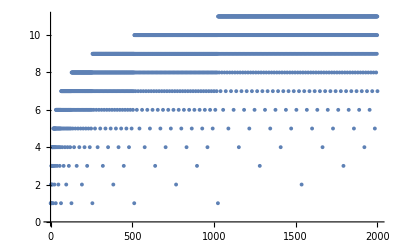

```mathematica
ListPlot[%]
```

```mathematica
Max[Map[Max,table]]
```

11

```mathematica
ArrayPlot[Map[PadRight[#,2000]&,table]]
```

-Graphics-

```mathematica
wegrh++
```

4

```mathematica
CellularAutomaton[124,{IntegerDigits[33,2],0},100][[50]]
```

{1,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
centaddlen[x_]:=Block[{calist=CellularAutomaton[124,{IntegerDigits[x,2],0},100]},Table[carrylen[FromDigits[calist[[i]],2],FromDigits[calist[[i+1]],2]],{i,1,100}]]
```

```mathematica
Timing[centaddlen[43]]
```

{0.33838,{2,6,1,2,2,4,4,3,2,7,5,2,2,4,4,3,5,6,3,2,7,5,4,3,2,7,7,3,2,4,4,4,7,6,3,3,7,5,7,4,2,7,7,7,7,4,4,4,5,6,10,3,7,5,5,4,7,7,7,7,4,4,4,4,5,6,10,4,7,5,5,4,6,7,7,7,5,4,4,5,6,6,10,4,7,5,6,4,6,7,7,7,4,5,12,4,5,6,10,4}}

```mathematica
Timing[bumptable=Monitor[Table[Sort[DeleteDuplicates[centaddlen[b]]],{b,1,2000}],b];]
```

```mathematica
ListPlot[Map[Length,bumptable]]
```

```mathematica
Map[Count[#,1]&,bumptable]
ListPlot[%]
```